## Utility

```mathematica
Labels[type_] := SortBy[StringDrop[StringSplit[#,"/"][[-1]],Switch[type,"m",-2,_,-3]]&/@FileNames[NotebookDirectory[]<>"/"<>type<>"/*."<>type],{Cutoff[#],U[#],J[#],NSites[#]}&];
Job[label_] := StringSplit[label,"_"][[1]];
BC[label_] := StringSplit[label,"_"][[2]];
NSites[label_] := ToExpression[StringSplit[label,"_"][[3]]];
MaxDim[label_] := ToExpression[StringSplit[label,"_"][[4]]];
Cutoff[label_] := StringSplit[label,"_"][[5]];
Prec[label_] := StringSplit[label,"_"][[6]];
J[label_] := StringSplit[label,"_"][[7]];
U[label_] := ToExpression[StringSplit[label,"_"][[8]]];
Charge[label_] := ToExpression[StringSplit[label,"_"][[9]]];
ReadData[label_,type_] := Module[{stream, str},
stream = OpenRead[NotebookDirectory[]<>"/"<>type<>"/"<>label<>"."<>type];
str = ReadString[stream];
Close[stream];
str = StringReplace[str,"e"->"*10^"];
If[type!="m"&&type≠"an",
str = "{" <> StringDrop[StringReplace[StringReplace[str,"\n"->""],",}"->"}"],-1]<> "}"//ToExpression
];
str//ToExpression
];
FitParameterWithError[parameter_] := Module[{ndig = -Floor[Log10[parameter[[2]]]]},
ToString[SetAccuracy[parameter[[1]],ndig+1]]<>"("<>ToString[Round[10^ndig*parameter[[2]]]]<>")"
];
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
SetOptions[ListLogLogPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
```

## Analysis

### Central charge from entanglement entropy

```mathematica
AnalyzeEE[name_] := Module[{len,Y,X,L,lm,c,A,x},
Y = ReadData[name,"ee"] ;
len = Length[Y];
X = Y[[-1]];
L = NSites[name]-If[BC[name]=="p",0,1];
X = Select[X, L/5<#[[1]]<L*4/5&];
If[BC[name]=="p",
lm = LinearModelFit[X,Log[L/π Sin[π x/L]]/3 ,x];,
If[job=="haagerup",X=Select[X,True||Mod[#[[1]],period]!=2&]];
lm = LinearModelFit[X,Log[L/π Sin[π (x-1/2)/L]]/6 ,x];
];
c = FitParameterWithError[lm["ParameterTableEntries"][[2]]];Show[ListPlot[#&/@Y,PlotMarkers->{"●",4},AxesLabel->{MaTeX["\\ell",Magnification->1.75],MaTeX["S_\\ell",Magnification->2]},(*PlotLabel->MaTeX["\\begin{array}{c} \\text{\\bf "<>If[BC[name]=="p","Periodic","Open"]<>"  } L="<>ToString[NSites[name]-If[BC[name]=="p",0,1]] <> "~~c="<>c<>" \\end{array}",Magnification->1.5],*)
(*PlotLabel->MaTeX["c="<>c,Magnification->1.75],*)
PlotStyle->({Opacity[1],RGBColor[#,1-#,0]}&/@Table[((k-1)/Max[len-1,1]),{k,1,len}])],
Plot[{lm[x]},{x,0,L},PlotStyle->{Black,Thick}]]
];
```

### Scaling dimension from energy

```mathematica
fitGSEnergy[gsEnergies_,minL_,bc_,show_,pbcGS_] := Module[{maxL,min,max,minE,maxE,GSEnergy,Energy},
(*lm = LinearModelFit[{#[[1]],#[[2]]}&/@Select[gsEnergies,#[[1]]≥minL&],{L,1,1/L},L];*)
lm = NonlinearModelFit[{#[[1]],#[[2]]}&/@Select[gsEnergies,#[[1]]≥minL&],α L+β+γ/L,{α,β,γ},L,MaxIterations->10000];
maxL = Max[Transpose[gsEnergies][[1]]]*1.01;
min = SortBy[gsEnergies,#[[2]]&][[2]];
max = SortBy[gsEnergies,#[[2]]&][[-2]];
(*minE = Floor[100*min[[2]]]/100;
maxE = Ceiling[100*max[[2]]]/100;*)
plot = Show[
ListPlot[{#[[1]],#[[2]]}&/@gsEnergies,Joined->False,PlotMarkers->{"●",6},PlotStyle->Black,
(*PlotLabel->MaTeX["\\text{\\bf "<>If[bc==="p","Periodic","Open"]<>"}",Magnification->1.5],*)
AxesLabel->{MaTeX["L",Magnification->1.7],MaTeX[show,Magnification->1.7]},PlotRange->Full,AxesOrigin->{0,Min[minE,0]}
],
Plot[lm[L],{L,6,maxL},PlotStyle->{Opacity[.3],Black,Thick}],
Plot[lm[L],{L,2.5,6},PlotStyle->{Opacity[.3],Black,Thick}]
];
Print[lm];
Print[lm["ParameterTable"]];
Print[ListPlot[
Transpose[{Select[Transpose[gsEnergies][[1]],#≥minL&],
lm["StandardizedResiduals"]
}]
]];
plot
];
```

```mathematica
fitGSEnergy[gsEnergies_,minL_,bc_,show_,pbcGS_] := Module[{maxL,min,max,minE,maxE,GSEnergy,Energy},
(*lm = LinearModelFit[{#[[1]],#[[2]]}&/@Select[gsEnergies,#[[1]]≥minL&],{L,1,1/L,1/Log[L]/L},L];*)
(*lm = NonlinearModelFit[{#[[1]],#[[2]]}&/@Select[gsEnergies,#[[1]]≥minL&],α L+β+γ/L+δ/L/(Log[L]+ϵ)^If[pbcGS,3,1],{α,β,γ},L,MaxIterations->10000];*)
lm = NonlinearModelFit[{#[[1]],#[[2]]}&/@Select[gsEnergies,#[[1]]≥minL&],α L+β+γ/L,{α,β,γ},L,MaxIterations->10000];
maxL = Max[Transpose[gsEnergies][[1]]]*1.01;
min = SortBy[gsEnergies,#[[2]]/#[[1]]&][[2]];
max = SortBy[gsEnergies,#[[2]]/#[[1]]&][[-2]];
minE = Floor[100*min[[2]]/min[[1]]]/100;
maxE = Ceiling[100*max[[2]]/max[[1]]]/100;
plot = Show[
ListPlot[{#[[1]],#[[2]]/#[[1]]}&/@gsEnergies,Joined->False,
PlotLabel->MaTeX["\\text{\\bf "<>If[bc==="p","Periodic","Open"]<>"}",Magnification->1.5],
AxesLabel->{MaTeX["L",Magnification->1.5],MaTeX["E_1/L",Magnification->1.5]},PlotRange->{{0,maxL},{minE,maxE}},AxesOrigin->{0,Min[minE,0]}
],
Plot[lm[L]/L,{L,0,maxL}]
];
If[show,
Print[lm["ParameterTable"]];
Print[plot];
];
(*GSEnergy[L0_] := lm[L0];*)
(*gsE = gsEnergies;*)
GSEnergy[L0_] := Select[gsEnergies,#[[1]]==L0&][[1,2]];
Energy[L0_,E0_] := (E0-GSEnergy[L0])*L0/If[bc=="p",12,24];(*(-lm["ParameterTableEntries"][[3,1]])**)
Energy
];
```

### Periodic spectral analysis

```mathematica
tol = 2*10^-1;
rs = {ζ,-1/ζ};
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[-1]]-r]/Abs[r]<tol&],{r,rs}]
,
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],And@@Table[Abs[#[[-1]]-r]/Abs[r]>tol,{r,rs}]&]
}
]
];

styles = {Black,{Black,Opacity[1]},Black};
markers = {{"●",8},{"○",6},{"○",6}};
height = 3;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots,min,st,em,tw,tw2,fe,fe1},
min = c*Energy[L,Select[spectrum[[2]],Abs[#[[2]]-2]<10^-3&][[1,1]]];
st = c*Select[spectrumByRho[[1]],Abs[#[[1]]-2]<10^-3&][[1,2]];
em = c*Select[spectrumByRho[[1]],Abs[#[[1]]-0]<10^-3&][[2,2]];
tw = c*Select[spectrumByRho[[1]],Abs[#[[1]]-L/3]<10^-3&][[1,2]];
tw2 = c*Select[spectrumByRho[[2]],Abs[#[[1]]-L/3]<10^-3&][[1,2]];

fe = c*Select[spectrumByRho[[2]],Abs[#[[1]]-0]<10^-3&][[1,2]];
fe1 = c*Select[spectrumByRho[[2]],Abs[#[[1]]-1]<10^-3&][[1,2]];

scalars[L] = #[[2]]/(fe1-fe)&/@(c*Select[spectrumByRho[[2]],Abs[#[[1]]-0]<10^-3&]);

plots = Table[ListPlot[{#[[1]],#[[2]]*c*(1/(fe1-fe))}&/@spectrumByRho[[i]],PlotMarkers->markers[[i]],PlotStyle->styles[[i]]],{i,1,3}];
ScaleFactor[L] = (1/(fe1-fe));
{min,st,em,tw,tw2,fe,fe1} = {min,st,em,tw,tw2,fe,fe1}*(1/(fe1-fe));
Print[st/2];

AppendTo[plots, Plot[{1,2,3,4},{x,-100,100},PlotStyle->{{Black,Dashed,Thin,Opacity[.3]}}]];
If[Mod[L,period]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin,Opacity[.3]}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin,Opacity[.3]}}]],{i,-Floor[L/2],L/2}];
AppendTo[plots,Plot[Abs[x]+fe,{x,0,1},PlotStyle->{Black,Dashed,Thin}]];

Show[Join[plots,
{Graphics[{FaceForm[],EdgeForm[{Red,Opacity[.7],Thick}],Rectangle[{1.9,min-.1},{2.1,2.1}]}],
Graphics[{FaceForm[],EdgeForm[{Blue,Opacity[.7],Thick}],Ellipsoid[{L/3,(tw+tw2)/2},{.2,.2+(tw-tw2)/2}]}](*Ellipsoid[{L/3,.575},{.2,.475}]}]*)}
],(*PlotLabel->plotLabel,*)AxesOrigin->{-.1,0},PlotRange->{{(*If[OddQ[L],-L/2,-L/2+1]*)-.1,Floor[L/2]},{0,height-.15}},AxesLabel->{MaTeX["p",Magnification->1.25],MaTeX["\\Delta",Magnification->1.25]},ImageSize->{Automatic,300},AspectRatio->height/Floor[L/2]]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==1600&&Cutoff[#]=="1e-08"&&J[#]==j&&U[#]==2&&Charge[#]===0&];
(*spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];*)
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,6,"p",False,True];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Show[
Spectrum[Energy,Spec[L0],cc,MaTeX["L="<>ToString[L0]<>"~~c="<>ToString[cc],Magnification->1.5]]
,
(*Plot[Abs[x],{x,0,100},Filling->Bottom,PlotStyle->None,ColorFunction->Function[{horiz,vert},Opacity[.2,Gray]]]*)
Plot[Abs[x],{x,0,4},PlotStyle->{Black,Dashed,Thin}]
]
]
```

### Periodic spectral analysis L=18

```mathematica
Graphics`PlotMarkers[]
```

{{●,10.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

```mathematica
tol = 2*10^-2;
tol = 2*10^-1;
rs = {ζ,-1/ζ};
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[-1]]-r]/Abs[r]<tol&],{r,rs}]
,
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],And@@Table[Abs[#[[-1]]-r]/Abs[r]>tol,{r,rs}]&]
}
]
];

styles = {Black,{Black,Opacity[1]},Black};
markers = {{"●",8},{"○",6},{"○",6}};
height = 3;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots,min,st,fe,fe1,tw,tw2},
min = c*Energy[L,Select[spectrum[[2]],Abs[#[[2]]-2]<10^-3&][[1,1]]];
st = c*Select[spectrumByRho[[2]],Abs[#[[1]]-2]<10^-3&][[1,2]];
fe = c*Select[spectrumByRho[[2]],Abs[#[[1]]-0]<10^-3&][[2,2]];
fe1 = c*Select[spectrumByRho[[2]],Abs[#[[1]]-1]<10^-3&][[1,2]];
tw = c*Select[spectrumByRho[[2]],Abs[#[[1]]-L/3]<10^-3&][[3,2]];
tw2 = c*Select[spectrumByRho[[2]],Abs[#[[1]]-L/3]<10^-3&][[1,2]];

scalars[L] = #[[2]]/(fe1-fe)&/@(c*Select[spectrumByRho[[2]],Abs[#[[1]]-0]<10^-3&]);

plots = Table[ListPlot[{#[[1]],#[[2]]*c*(1/(fe1-fe))}&/@spectrumByRho[[i]],PlotMarkers->markers[[i]],PlotStyle->styles[[i]]],{i,1,3}];
ScaleFactor[L] = (1/(fe1-fe));
{min,st,fe,tw,tw2} = {min,st,fe,tw,tw2}*(1/(fe1-fe));

AppendTo[plots, Plot[{1,2,3,4},{x,-100,100},PlotStyle->{{Black,Dashed,Thin,Opacity[.3]}}]];
If[Mod[L,period]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin,Opacity[.3]}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin,Opacity[.3]}}]],{i,-Floor[L/2],L/2}];
AppendTo[plots,Plot[Abs[x]+fe,{x,0,1},PlotStyle->{Black,Dashed,Thin}]];

Show[Join[plots,
{Graphics[{FaceForm[],EdgeForm[{Red,Opacity[.7],Thick}],Rectangle[{1.9,min-.1},{2.1,2.1}]}]
,
Graphics[{FaceForm[],EdgeForm[{Blue,Opacity[.7],Thick}],Ellipsoid[{L/3,(tw+tw2)/2},{.2,.2+(tw-tw2)/2}]}]
}
],(*PlotLabel->plotLabel,*)AxesOrigin->{-.1,0},PlotRange->{{(*If[OddQ[L],-L/2,-L/2+1]*)-.1,Floor[L/2]},{0,height-.15}},AxesLabel->{MaTeX["p",Magnification->1.25],MaTeX["\\Delta",Magnification->1.25]},ImageSize->{Automatic,300},AspectRatio->height/Floor[L/2]]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==1600&&Cutoff[#]=="1e-08"&&J[#]==j&&U[#]==2&&Charge[#]===0&];
(*spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];*)
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,6,"p",False,True];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Show[
Spectrum[Energy,Spec[L0],cc,MaTeX["L="<>ToString[L0]<>"~~c="<>ToString[cc],Magnification->1.5]]
,
(*Plot[Abs[x],{x,0,100},Filling->Bottom,PlotStyle->None,ColorFunction->Function[{horiz,vert},Opacity[.2,Gray]]]*)
Plot[Abs[x],{x,0,4},PlotStyle->{Black,Dashed,Thin}]
]
]
```

### Periodic spectral analysis Q=1

```mathematica
tol = 2*10^-2;
tol = 2*10^-1;
rs = {ζ,-1/ζ};
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[-1]]-r]/Abs[r]<tol&],{r,rs}]
,
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],And@@Table[Abs[#[[-1]]-r]/Abs[r]>tol,{r,rs}]&]
}
]
];

styles = {Black,{Black,Opacity[1]},Black};
markers = {{"●",8},{"○",6},{"○",6}};
height = 3.5;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots,min,st,em,em1,tw,tw2},
plots = Table[ListPlot[{#[[1]],#[[2]]*c*ScaleFactor[L]}&/@spectrumByRho[[i]],PlotMarkers->markers[[i]],PlotStyle->styles[[i]]],{i,1,3}];

AppendTo[plots, Plot[{1,2,3,4},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
If[Mod[L,period]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin}}]],{i,-Floor[L/2],L/2}];
AppendTo[plots,Plot[Abs[x]+em,{x,0,1},PlotStyle->{Black,Dashed,Thin}]];

Show[
(*Join[plots,
{Graphics[{FaceForm[],EdgeForm[{Blue,Opacity[.7],Thick}],Rectangle[{1.9,min-.1},{2.1,2.1}]}]
,
Graphics[{FaceForm[],EdgeForm[{Red,Opacity[.7],Thick}],Ellipsoid[{L/3,(tw+tw2)/2},{.2,.2+(tw-tw2)/2}]}]
}
]*)plots
,
AxesOrigin->{-.1,0},PlotRange->{{(*If[OddQ[L],-L/2,-L/2+1]*)-.1,Floor[L/2]},{0,height}},AxesLabel->{MaTeX["p",Magnification->1.25],MaTeX["\\Delta",Magnification->1.25]},ImageSize->{Automatic,300},AspectRatio->height/Floor[L/2]]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==1600&&Cutoff[#]=="1e-08"&&J[#]==j&&U[#]==2&&Charge[#]===0&];
(*spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];*)
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,6,"p",False,True];
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Show[
Spectrum[Energy,Spec[L0],cc,MaTeX["L="<>ToString[L0]<>"~~c="<>ToString[cc],Magnification->1.5]]
(*,
(*Plot[Abs[x],{x,0,100},Filling->Bottom,PlotStyle->None,ColorFunction->Function[{horiz,vert},Opacity[.2,Gray]]]*)
Plot[Abs[x],{x,0,4},PlotStyle->{Black,Dashed,Thin}]*)
]
]

ModularInvariance[L0_,j_] := Module[{},
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==1600&&Cutoff[#]=="1e-08"&&J[#]==j&&U[#]==2&&Charge[#]===0&];
(*spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];*)
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,6,"p",False,True];

spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===3&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
spectrumByRho = CollectByRho[Energy,Spec[L0]];
spec0 = Flatten[Table[{#[[1]],#[[2]]*cc*ScaleFactor[L0]}&/@spectrumByRho[[i]],{i,1,3}],1];

spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===4&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
spectrumByRho = CollectByRho[Energy,Spec[L0]];
spec1 = Flatten[Table[{#[[1]],#[[2]]*cc*ScaleFactor[L0]}&/@spectrumByRho[[i]],{i,1,3}],1];

spec = {Round[#[[1]]],#[[2]]}&/@Join[spec0, spec1,{-#[[1]],#[[2]]}&/@spec1];
(*spec = {Round[#[[1]]],#[[2]]}&/@Join[spec0];*)
spec = Flatten[If[#[[1]]==0||#[[1]]==L0/2,{#},{#,{-#[[1]],#[[2]]}}]&/@spec,1];
spec = Select[spec,#[[2]]≤3&];

Z = Total[qq^((#[[2]]-#[[1]])/2)qqb^((#[[2]]+#[[1]])/2)&/@spec]/(qq qqb)^(CC/24)/.{qq->Exp[2π ⅈ τ],qqb->Exp[-2π ⅈ τb]}/.{τ->x+ⅈ y,τb->x-ⅈ y}//PowerExpand;

fcn = Chop[D[Z/.{x->0,y->Exp[z]},z]/.z->0];
c0 = CC/.FindRoot[fcn,{CC,2}];
Print[c0];

Z/.{CC->cc}/.{x->0,y->Exp[z]}

(*Plot[Z/.{CC->cc}/.{x->0,y->Exp[z]},{z,-1,1},PlotRange->Automatic,AxesLabel->{MaTeX["\\log\\tau_2",Magnification->1.25],MaTeX["Z",Magnification->1.25]},PlotLabel->MaTeX["c="<>ToString[c0],Magnification->1.25]]*)
]
```

### Periodic spectral analysis shift-Z3

```mathematica
tol = 2*10^-2;
tol = 2*10^-1;
rs = {ζ,-1/ζ};
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[-1]]-r]/Abs[r]<tol&],{r,rs}]
,
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],And@@Table[Abs[#[[-1]]-r]/Abs[r]>tol,{r,rs}]&]
}
]
];

styles = {Black,{Black,Opacity[1]},Black};
markers = {{"●",8},{"○",6},{"○",6}};
height = 3.5;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{Energy2,L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots,min,st,em,tw,tw2,fe,fe1,s,km},
(*min = c*Energy[L,Select[spectrum[[2]],Abs[#[[2]]-2]<10^-3&][[1,1]]];
st = c*Select[spectrumByRho[[1]],Abs[#[[1]]-2]<10^-3&][[1,2]];
em = c*Select[spectrumByRho[[1]],Abs[#[[1]]-0]<10^-3&][[2,2]];
tw = c*Select[spectrumByRho[[1]],Abs[#[[1]]-L/3]<10^-3&][[1,2]];
tw2 = c*Select[spectrumByRho[[2]],Abs[#[[1]]-L/3]<10^-3&][[1,2]];*)

(*fe = c*Select[spectrumByRho[[2]],Abs[#[[1]]-0]<10^-3&][[1,2]];
fe1 = c*Select[spectrumByRho[[2]],Abs[#[[1]]-1]<10^-3&][[1,2]];*)

(*fe = {spectrumByRho[[1,1,1]],c*spectrumByRho[[1,1,2]]};
fe1 = c*Select[spectrumByRho[[1]],Abs[#[[1]]-(fe[[1]]-1)]<10^-3&][[1,2]];*)

s = If[Mod[L,3]==1,Ceiling[L/3],Floor[L/3]];
fe = {s,c*Energy[L,Select[spectrum[[2]],Abs[#[[2]]-s]<10^-3&][[1,1]]]};
(*fe1 = c*Select[spectrumByRho[[1]],Abs[#[[1]]-(fe[[1]]-1)]<10^-3&][[1,2]];*)
km = c*Select[spectrumByRho[[2]],Abs[#[[1]]-1]<10^-3&][[1,2]];

(*km = fe1-fe[[2]];

glsmParams = Transpose[gslm["ParameterTableEntries"]][[1]];
gslm2[x_] := glsmParams[[1]]x+glsmParams[[2]]-km*c/x;
Energy2[L0_,E0_] := (E0-gslm2[L0])*L0/If[bc=="p",12,24];
spectrumByRho = CollectByRho[Energy2,spectrum];*)

scalars[L] = #[[2]]/km&/@(c*Select[spectrumByRho[[2]],Abs[#[[1]]-0]<10^-3&]);

(*plots = Table[ListPlot[{#[[1]],#[[2]]*c*(1/(fe1-fe[[2]]))}&/@spectrumByRho[[i]],PlotMarkers->markers[[i]],PlotStyle->styles[[i]]],{i,1,3}];
ScaleFactor[L] = (1/(fe1-fe[[2]]));*)

plots = Table[ListPlot[{#[[1]],#[[2]]*c*(1/km)}&/@spectrumByRho[[i]],PlotMarkers->markers[[i]],PlotStyle->styles[[i]]],{i,1,3}];
ScaleFactor[L] = (1/km);

(*{fe,fe1} = {fe,fe1}*(1/(fe1-fe));*)
(*{min,st,em,tw,tw2,fe,fe1} = {min,st,em,tw,tw2,fe,fe1}*(1/(fe1-fe));
Print[st/2];*)

AppendTo[plots, Plot[{1,2,3,4},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
If[Mod[L,period]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin}}]],{i,-Floor[L/2],L/2}];
(*AppendTo[plots,Plot[Abs[x-fe[[1]]]+fe[[2]]*(1/(fe1-fe[[2]])),{x,fe[[1]]-1,fe[[1]]+1},PlotStyle->{Black,Dashed,Thin}]];*)
AppendTo[plots,Plot[Abs[x-fe[[1]]]+fe[[2]]*(1/km),{x,fe[[1]]-1,fe[[1]]+1},PlotStyle->{Black,Dashed,Thin}]];

Show[Join[plots
(*,
{Graphics[{FaceForm[],EdgeForm[{Blue,Opacity[.7],Thick}],Rectangle[{1.9,min-.1},{2.1,2.1}]}],
Graphics[{FaceForm[],EdgeForm[{Red,Opacity[.7],Thick}],Ellipsoid[{L/3,(tw+tw2)/2},{.2,.2+(tw-tw2)/2}]}](*Ellipsoid[{L/3,.575},{.2,.475}]}]*)}
*)
],(*PlotLabel->plotLabel,*)AxesOrigin->{-.1,0},PlotRange->{{(*If[OddQ[L],-L/2,-L/2+1]*)-.1,Floor[L/2]},{0,height}},AxesLabel->{MaTeX["p",Magnification->1.25],MaTeX["\\Delta",Magnification->1.25]},ImageSize->{Automatic,300},AspectRatio->height/Floor[L/2]]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
(*spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==1600&&Cutoff[#]=="1e-08"&&J[#]==j&&U[#]==2&&Charge[#]===0&];
(*spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];*)
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,6,"p",False,True];*)

spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy[L0,E0_] := (E0-gslm[L0])(**L0*)(*/If[bc=="p",12,24]*)(*/SF[L0]*);
(*Energy[L0,E0_] := (E0-GSInterpolation [L0])*L0/If[bc=="p",12,24](*/SF[L0]*);*)
Show[
Spectrum[Energy,Spec[L0],cc,MaTeX["L="<>ToString[L0]<>"~~c="<>ToString[cc],Magnification->1.5]]
,
(*Plot[Abs[x],{x,0,100},Filling->Bottom,PlotStyle->None,ColorFunction->Function[{horiz,vert},Opacity[.2,Gray]]]*)
Plot[Abs[x],{x,0,4},PlotStyle->{Black,Dashed,Thin}]
]
]
```

### Periodic spectral analysis shift-Z3

```mathematica
tol = 2*10^-1;
rs = {ζ,-1/ζ};
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],Length[#]==3&&Abs[#[[-1]]-r]/Abs[r]<tol&],{r,rs}]
,
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],And@@Table[Abs[#[[-1]]-r]/Abs[r]>tol,{r,rs}]&]
}
]
];

styles = {Black,{Black,Opacity[1]},Black};
markers = {{"●",8},{"○",6},{"○",6}};
height = 3;
Spectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{Energy2,L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots,min,st,em,tw,tw2,fe,fe1,s,km,v},
s = If[Mod[L,3]==1,Ceiling[L/3],Floor[L/3]];
fe = {s,Energy[L,Select[spectrum[[2]],Abs[#[[2]]-s]<10^-3&][[1,1]]]};
fe1 = Select[spectrumByRho[[1]],Abs[#[[1]]-(fe[[1]]-1)]<10^-3&][[1,2]];
km = Select[spectrumByRho[[2]],Abs[#[[1]]-1]<10^-3&][[1,2]];
km = fe1-fe[[2]]; (* energy difference corresponding to Δ difference of 1 *)
v = km * L;

glsmParams = Transpose[gslm["ParameterTableEntries"]][[1]];
gslm2[x_] := glsmParams[[1]]x+glsmParams[[2]]+v*(-c/12)/x;
Energy2[L0_,E0_] := (E0-gslm2[L0])*L0/v(*/If[bc=="p",12,24]*);
spectrumByRho = CollectByRho[Energy2,spectrum];
fe = {s,Energy2[L,Select[spectrum[[2]],Abs[#[[2]]-s]<10^-3&][[1,1]]]};

scalars[L] = #[[2]]&/@(Select[spectrumByRho[[2]],Abs[#[[1]]-0]<10^-3&]);


plots = Table[ListPlot[{#[[1]],#[[2]]}&/@spectrumByRho[[i]],PlotMarkers->markers[[i]],PlotStyle->styles[[i]]],{i,1,3}];

AppendTo[plots, Plot[{1,2,3,4},{x,-100,100},PlotStyle->{{Black,Dashed,Thin,Opacity[.3]}}]];
If[Mod[L,period]≠0,
AppendTo[plots, Plot[{1/3,2/3},{x,-100,100},PlotStyle->{{Black,Dashed,Thin,Opacity[.3]}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin,Opacity[.3]}}]],{i,-Floor[L/2],L/2}];
AppendTo[plots,Plot[Abs[x-fe[[1]]]+fe[[2]],{x,fe[[1]]-1,fe[[1]]+1},PlotStyle->{Black,Dashed,Thin}]];

Show[Join[plots],AxesOrigin->{-.1,0},PlotRange->{{-.1,Floor[L/2]},{0,height-.15}},AxesLabel->{MaTeX["p",Magnification->1.25],MaTeX["\\Delta",Magnification->1.25]},ImageSize->{Automatic,300},AspectRatio->height/Floor[L/2]]
];

SpectrumIncludingFit[L0_,j_,q_] := Module[{},
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
Energy[L0,E0_] := (E0-gslm[L0])(**L0*)(*/If[bc=="p",12,24]*)(*/SF[L0]*);
Show[
Spectrum[Energy,Spec[L0],cc,MaTeX["L="<>ToString[L0]<>"~~c="<>ToString[cc],Magnification->1.5]]
,
Plot[Abs[x],{x,0,4},PlotStyle->{Black,Dashed,Thin}]
]
]
```

### Open spectral analysis

```mathematica
tol = 1*10^-2;
CollectByRho[Energy_,spectrum_] := Module[{L = spectrum[[1]]},
Join[
Table[{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],(*Length[#]==3&&*)Abs[#[[-1]]-r]/Abs[r]<tol&],{r,rs}]
,
{{#[[2]],Energy[L,#[[1]]]}&/@Select[spectrum[[2]],And@@Table[Abs[#[[-1]]-r]/Abs[r]>tol,{r,rs}]&]
}
]
];

styles = {Black,Black,Black,Black,Black};
markers = {"○","○","○","○","●"};
height = 2.5;
OpenSpectrum[Energy_,spectrum_,c_,plotLabel_] := Module[{data,L=spectrum[[1]],spectrumByRho = CollectByRho[Energy,spectrum],plots},
(*data = Table[{i-1,#[[2]]*c}&/@spectrumByRho[[i]],{i,1,Length[rs]+1}];*)
data = Table[{i-1,#[[2]]*c}&/@Select[spectrumByRho[[i]],#[[2]]*c<2.5&],{i,1,Length[rs]}];
data = DeleteCases[data,{}];
plots = {ListPlot[data,PlotMarkers->({#,9}&/@markers),PlotStyle->styles,Ticks->{{{0,MaTeX["\\text{I}",Magnification->1.25],0},{1,MaTeX["\\text{II}",Magnification->1.25],0},{2,MaTeX["\\text{III}",Magnification->1.25],0},{3,MaTeX["\\text{IV}",Magnification->1.25],0}}[[1;;Length[rs]]],Automatic}]};
Do[
AppendTo[plots, Plot[spectrumByRho[[i,1,2]]*c+If[i==1,2,1],{x,i-1-0.05,i-1+0.05},PlotStyle->{{Black}}]];
,{i,1,Length[rs]}
];
If[Mod[L,period]==0,
AppendTo[plots, Plot[{1,2},{x,-100,100},PlotStyle->{{Black,Dashed,Thin}}]];
];
Do[AppendTo[plots,ParametricPlot[{i,y},{y,0,height},PlotStyle->{{Black,Dashed,Thin}}]],{i,0,3}];
Show[plots,(*PlotLabel->plotLabel,*)AxesOrigin->{-.25,0},PlotRange->{{-.5,Length[rs]+.25-1},{0,height}},AxesLabel->{"",MaTeX["\\Delta",Magnification->1.25]},ImageSize->{Automatic,300},AspectRatio->1]
];

OpenSpectrumIncludingFit[L0_,j_,q_,cutoff_] := Module[{},
spectra = {NSites[#]-1,ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]=="1e-10"&&J[#]==j&&U[#]==2&&Charge[#]===0&];
(*spectra = {NSites[#]-1,ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];*)
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,minL,"d",False,False];
spectra = {NSites[#]-1,ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
OpenSpectrum[Energy,Spec[L0],cc,MaTeX["L="<>ToString[L0]<>"~~c="<>ToString[cc],Magnification->1.5]]
]
```

## Haagerup

### Antiferromagnetic

```mathematica
lm = LinearModelFit[Transpose[{Range[3,12],Log[{2,7,6,12,15,36,45,84,134,253}]}],{L,1},L]
```

FittedModel[-0.551569+0.498556 L]

```mathematica
Exp[lm["ParameterTableEntries"][[1,1]]]
```

1.64634

```mathematica
Exp[lm["ParameterTableEntries"][[2,1]]]
```

0.576046

```mathematica
Table[Exp[lm["ParameterTableEntries"][[1,1]]]^n,{n,3,12}]*Exp[lm["ParameterTableEntries"][[2,1]]]
```

{2.5705,4.23192,6.96718,11.4704,18.8841,31.0897,51.1844,84.2669,138.732,228.401}

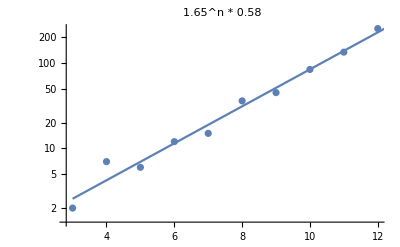

```mathematica
Show[
ListLogPlot[{Range[3,12],{2,7,6,12,15,36,45,84,134,253}}//Transpose],
Plot[lm[x],{x,3,13}],
PlotLabel->"1.65^n * 0.58"
]
```

### Global variables

```mathematica
period = 3;
ζ = (3+Sqrt[13])/2;
{job,bc,maxdim,cutoff,j,u,q} = {"haagerupq","p",1600,"1e-08","0,-1,0",2,0};
rs = If[bc=="p",{ζ,-1/ζ},{1,-0.322,-0.535,0.554}];
cc = 2;
minL = 18;
```

```mathematica
period = 3;
ζ = (3+Sqrt[13])/2;
{job,bc,maxdim,cutoff,j,u,q} = {"haagerup","d",1600,"1e-12","0,-1,0",2,0};
rs = If[bc=="p",{ζ,-1/ζ},{1,-0.322,-0.535,0.554}];
cc = 2;
minL = 18;
```

### Dynamical exponent

```mathematica
(*
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,1]]-#[[2,1,1]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
*)
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,2]]-#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&&Length[#[[2]]]>1&];
maxL = Max[Transpose[gaps][[1]]];
gaps = Select[gaps,#[[1]]≥maxL/2&];
logGaps = {Log[#[[1]]],Log[#[[2]]]}&/@gaps;
lm = LinearModelFit[{#[[1]],#[[2]]}&/@logGaps,L,L];
c = FitParameterWithError[lm["ParameterTableEntries"][[1]]];
z = FitParameterWithError[lm["ParameterTableEntries"][[2]]];
```

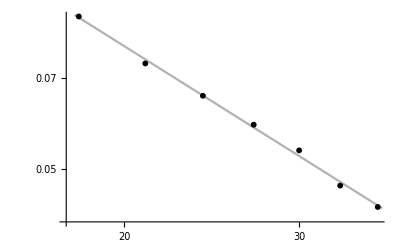

```mathematica
plot = Show[
ListLogLogPlot[gaps,(*Ticks->{Automatic,{0.015,0.02,0.025}},*)PlotMarkers->{"●",6},PlotStyle->Black,AxesLabel->{MaTeX["L",Magnification->1.75],MaTeX["\\Delta E",Magnification->1.75]}
(*,PlotLabel->MaTeX["\\begin{array}{c} \\text{\\bf "<>If[bc=="p","Periodic","Open"]<>"} \\\\ \\log(\\Delta E) = "<>z<>" \\log(L) + "<>c<>" \\end{array}"*)
(*,PlotLabel->MaTeX["\\log(\\Delta E) = "<>z<>" \\log(L) + "<>c,Magnification->1.75]*)],
Plot[lm[L],{L,Log[maxL/2]-0.01,Log[maxL]+0.01},PlotStyle->{Black,Opacity[.3]}]
]
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/puredyn.pdf",plot];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/puredynOpen.pdf",plot];
```

### Central charge from entanglement entropy

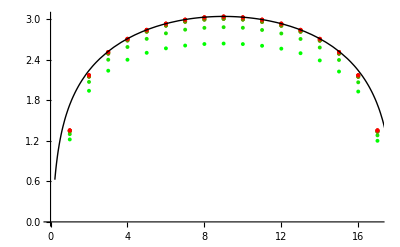

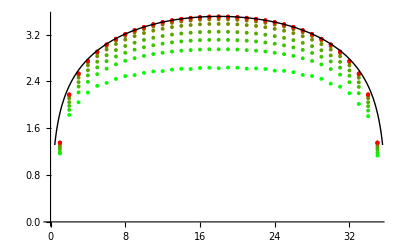

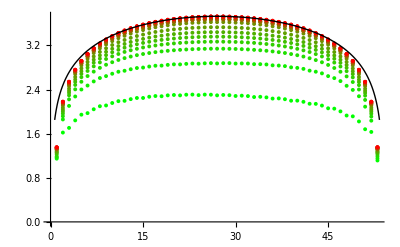

```mathematica
plots = AnalyzeEE[#]&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&&IntegerQ[(NSites[#]-If[BC[#]=="p",0,1])/If[BC[#]=="p",18,36]]&];
Print[#]&/@plots;
```

```mathematica
(*Export["/Users/yinhslin/git/haagerup-chain/haagerup/ee36Alt.pdf",plots[[2]]];*)
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/ee18.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/ee36.pdf",plots[[2]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen36.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen72.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen108.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen144.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen36Alt.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen72Alt.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen108Alt.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen144Alt.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen36All.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen72All.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen108All.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen144All.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/ee18_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/ee36_1,-1,0.pdf",plots[[2]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen36_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen72_1,-1,0.pdf",plots[[2]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen36Alt_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/eeOpen72Alt_1,-1,0.pdf",plots[[2]]];
```

### Scaling dimension from energy

```mathematica
Graphics`PlotMarkers[]
```

{{●,10.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

```mathematica
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===3&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
GSInterpolation = Interpolation[gsEnergies];

spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===3&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
ed = ListPlot[gsEnergies,PlotStyle->Red,PlotMarkers->{"□",12}];
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,2]]-#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
edGaps = ListPlot[gaps,PlotStyle->Red,PlotMarkers->{"□",12}];
```

FittedModel[-0.00485338-1.09789/L-0.845209 L]

| Estimate | Standard Error | t-Statistic | P-Value
α | -0.845209 | 0.000015906 | -53137.7 | 7.52559×10^-19
β | -0.00485338 | 0.000830347 | -5.84501 | 0.00427252
γ | -1.09789 | 0.0103688 | -105.884 | 4.77067×10^-8

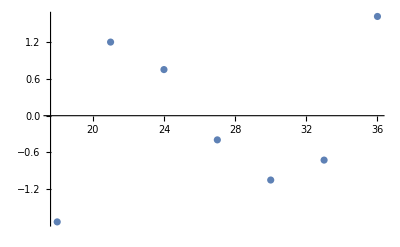

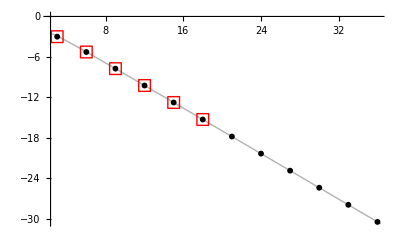

FittedModel[0.00394166+1.53372/L-0.0000855091 L]

| Estimate | Standard Error | t-Statistic | P-Value
α | -0.0000855091 | 0.000293959 | -0.290888 | 0.785596
β | 0.00394166 | 0.0153456 | 0.256859 | 0.809959
γ | 1.53372 | 0.191626 | 8.00372 | 0.00132156

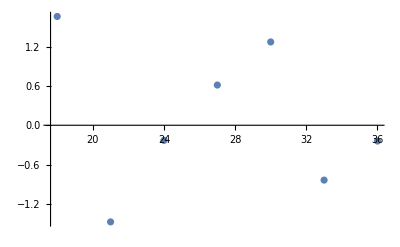

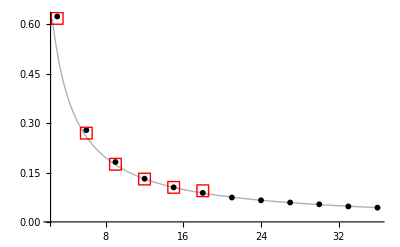

```mathematica
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
plot = fitGSEnergy[gsEnergies,minL,bc,"E_0",If[bc=="p",True,False]];
gslm = lm;
fig1 = Show[plot,ed]
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,2]]-#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&&Length[#[[2]]]>1&];
plotGaps = fitGSEnergy[gaps,minL,bc,"\\Delta E",False];
fig2 = Show[plotGaps,edGaps]
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/E0vsL.pdf",fig1];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/GapvsL.pdf",fig2];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/E0vsLOpen.pdf",fig1];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/GapvsLOpen.pdf",fig2];
```

```mathematica
(*
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,1]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
*)
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
Energy = fitGSEnergy[gsEnergies,minL,bc,True];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/energy.pdf",plot];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/energyOpen.pdf",plot];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/energy_1,-1,0.pdf",plot];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/energyOpen_1,-1,0.pdf",plot];
```

```mathematica
tmp = {#[[1]],#[[2]]-(-.845022*#[[1]]-0.016408300547179934)}&/@gsEnergies
```

{{6,-0.18544},{9,-0.115918},{12,-0.0834657},{15,-0.0648141},{18,-0.0528437},{21,-0.0446093},{24,-0.0386602},{27,-0.0341944},{30,-0.0307315},{33,-0.0279679},{36,-0.0257022},{39,-0.0237978},{42,-0.0221604},{45,-0.0207212},{48,-0.0194339},{51,-0.0182626},{54,-0.01718},{57,-0.0161697},{60,-0.0152163},{63,-0.0143078},{69,-0.0126009},{72,-0.0117911}}

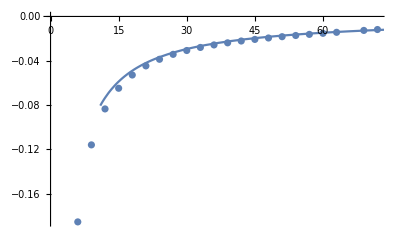

```mathematica
Show[ListPlot[tmp],Plot[-0.8815787426674647/L,{L,0,140}]]
```

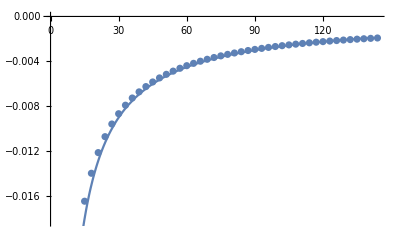

```mathematica
Show[ListPlot[tmp],Plot[-0.27020610534143374/L,{L,0,140}]]
```

```mathematica
Style[Grid[SetPrecision[{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {L, -0.845340141791173, 2.9988882305250073*^-7, -2.8188451079524946*^6, 7.066278450703662*^-244}, 
    {1, 0.5944168801783598, 0.000039735081735906595, 14959.498111242468, 4.795337003253419*^-146}, {1/L, -0.27020610534143374, 0.0010813202925317718, -249.8853551603855, 
     1.2391199936917967*^-69}, {1/L^2, 0.34995358226780343, 0.005919045780473086, 59.123310622516094, 8.035308546354648*^-43}},3], Alignment -> {Left, Automatic}, 
   Dividers -> {{2 -> GrayLevel[0.7]}, {2 -> GrayLevel[0.7]}}, ItemSize -> {Automatic, Automatic}, Spacings -> {{2 -> 1}, {2 -> 0.75}}], "DialogStyle"]//TeXForm
```

NumberForm::sigz: Number precision is lower than number of digits shown; padding with zeros.

\begin{array}{l|llll}
 \text{} & \text{Estimate} & \text{Standard Error} & \text{t-Statistic} & \text{P-Value} \\
\hline
 L & -0.845 & \text{2.998888230525$\grave{ }$3.*${}^{\wedge}$-7} & -2.82\times 10^6 & \text{7.06627845070366164569901482$\grave{ }$3.*${}^{\wedge}$-244} \\
 1.00 & 0.594 & 0.0000397 & 15000. & \text{4.795337003253419148638884809$\grave{ }$3.*${}^{\wedge}$-146} \\
 \frac{1}{L} & -0.270 & 0.00108 & -250. & \text{1.239119993691796653871688826$\grave{ }$3.*${}^{\wedge}$-69} \\
 \frac{1}{L^2} & 0.350 & 0.00592 & 59.1 & \text{8.035308546354648$\grave{ }$3.*${}^{\wedge}$-43} \\
\end{array}

```mathematica
Style[Grid[SetPrecision[{{"", "Estimate", "Standard Error", "t-Statistic", "P-Value"}, {L, -0.000013310530749469586, 0.000031476430886360515, -0.4228729361827791, 
     0.6771354967003513}, {1, 0.0017969393842059078, 0.0024970081134147826, 0.7196369825761215, 0.4805076975833976}, 
    {1/L, 2.0318500691758765, 0.048530339104059246, 41.867625627324855, 3.5233828375919483*^-20}, {1/L^2, -2.3028314392623015, 0.2273063745768709, -10.130958463215142, 
     4.266142055652015*^-9}},3], Alignment -> {Left, Automatic}, Dividers -> {{2 -> GrayLevel[0.7]}, {2 -> GrayLevel[0.7]}}, ItemSize -> {Automatic, Automatic}, 
   Spacings -> {{2 -> 1}, {2 -> 0.75}}], "DialogStyle"]//TeXForm
```

\begin{array}{l|llll}
 \text{} & \text{Estimate} & \text{Standard Error} & \text{t-Statistic} & \text{P-Value} \\
\hline
 L & -0.0000133 & 0.0000315 & -0.423 & 0.677 \\
 1.00 & 0.00180 & 0.00250 & 0.720 & 0.481 \\
 \frac{1}{L} & 2.03 & 0.0485 & 41.9 & \text{3.523382837591948313$\grave{ }$3.*${}^{\wedge}$-20} \\
 \frac{1}{L^2} & -2.30 & 0.227 & -10.1 & \text{4.26614205565201484803038436077$\grave{ }$3.*${}^{\wedge}$-9} \\
\end{array}

### Periodic spectral analysis

0.979287

1.00036

0.999231

0.996888

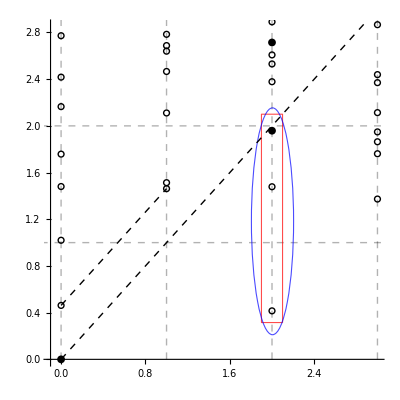

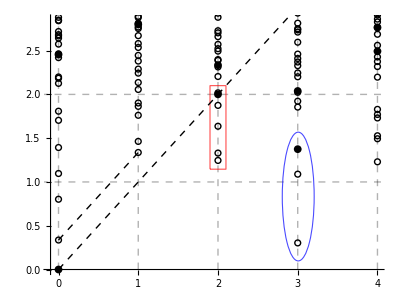

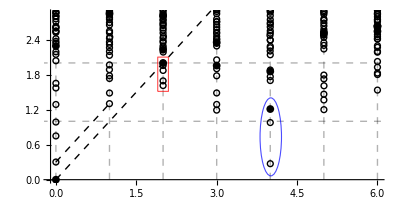

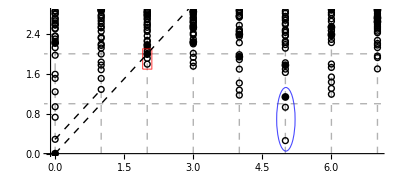

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,3],{L0,6,15,period}]//Flatten;
Print[#]&/@plots;
```

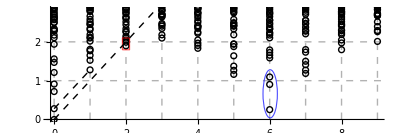

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,3],{L0,18,18,period}]//Flatten;
Print[#]&/@plots;
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec18_ed.pdf",plots[[1]]];
```

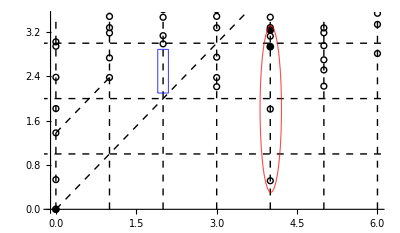

```mathematica
If[bc!="p",
Print["Change bc"];
,
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,12,12,period}]//Flatten;
Print[#]&/@plots;
]
```

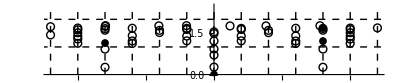

```mathematica
If[bc!="p",
Print["Change bc"];
,
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,12,12,period}]//Flatten;
Print[#]&/@plots;
]
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec6_ed.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec9_ed.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec12_ed.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec15_ed.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec6_edAlt.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec9_edAlt.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec12_edAlt.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec15_edAlt.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec6.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec9.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec12.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec15.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec6_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec9_1,-1,0.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec12_1,-1,0.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec15_1,-1,0.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/specq6.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/specq9.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/specq12.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/specq15.pdf",plots[[4]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec8.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec11.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec14.pdf",plots[[3]]];
```

### Periodic spectral analysis Q=1

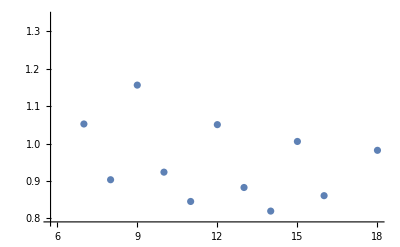

```mathematica
plot = ListPlot[Table[{L,ScaleFactor[L]},{L,6,18}],AxesLabel->{MaTeX["L",Magnification->1.5],MaTeX["\\gamma",Magnification->1.5]}]
```

```mathematica
SF = Interpolation[Table[{L,ScaleFactor[L]},{L,6,18,3}]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/gamma.pdf",plot];
```

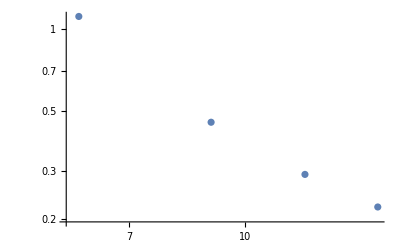

```mathematica
plot = ListLogLogPlot[{Range[6,15,3],2*{0.5546427695508573,
0.22716113750079947,
0.1462637871948819,
0.11111221362728643}}//Transpose,AxesLabel->{MaTeX["L",Magnification->1.5],MaTeX["\\Delta_\\text{em} - 2",Magnification->1.5]}]
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/em.pdf",plot];
```

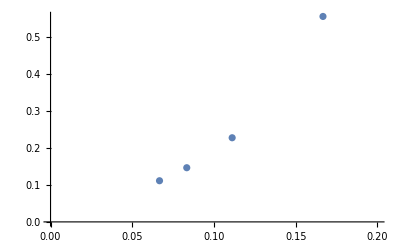

```mathematica
ListPlot[{1/Range[6,15,3],{0.5546427695508573,
0.22716113750079947,
0.1462637871948819,
0.11111221362728643}}//Transpose,PlotRange->{{0,.2},Automatic}]
```

```mathematica
Zs = Table[Log[ModularInvariance[L0,j]],{L0,6,18,3}];
```

1.90811

2.54538

2.26618

2.04458

2.06519

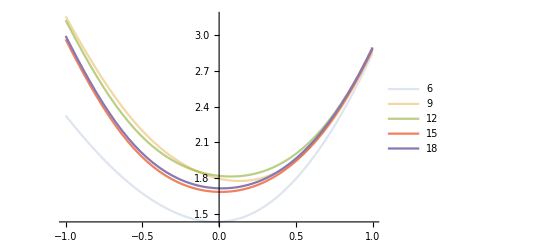

```mathematica
plot = Plot[Zs,{z,-1,1},PlotRange->Automatic,AxesLabel->{MaTeX["\\log\\tau_2",Magnification->1.25],MaTeX["\\log Z",Magnification->1.25]},PlotLegends->{Range[6,18,3]},PlotStyle->Table[Opacity[k/5],{k,1,5}]]
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/mod_inv.pdf",plot];
```

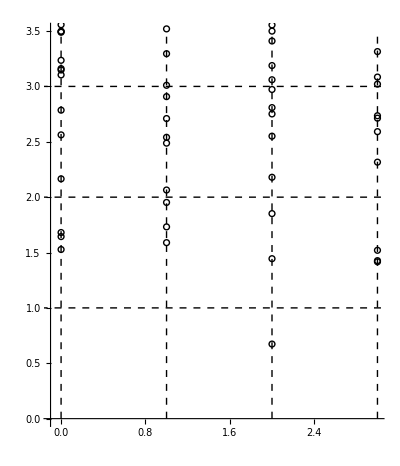

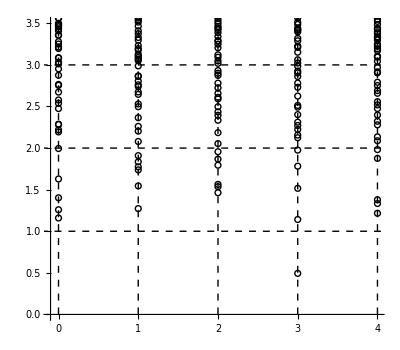

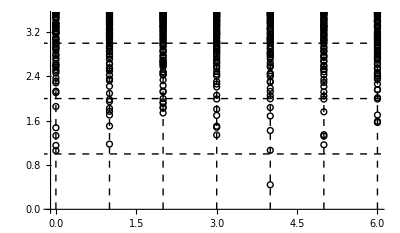

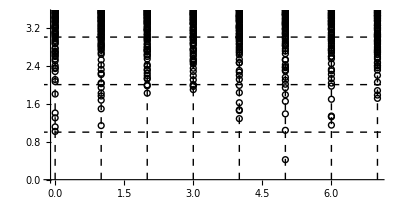

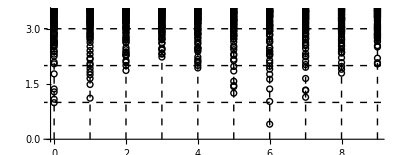

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,4],{L0,6,18,period}]//Flatten;
Print[#]&/@plots;
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec6_ed_Q.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec9_ed_Q.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec12_ed_Q.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec15_ed_Q.pdf",plots[[4]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec18_ed_Q.pdf",plots[[5]]];
```

### Periodic spectral analysis Z3 twisted

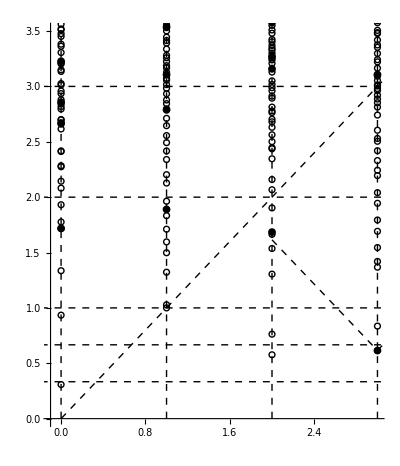

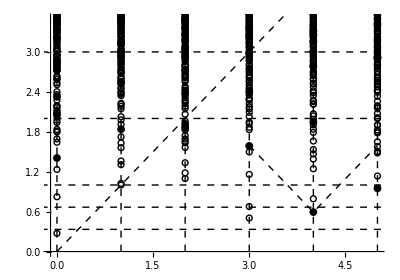

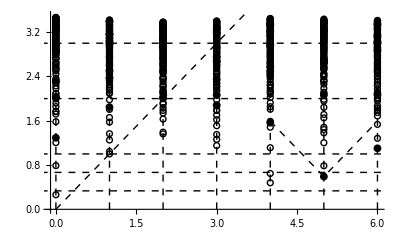

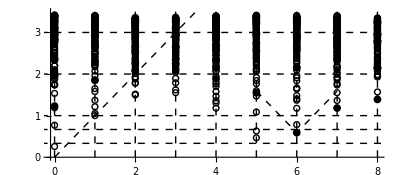

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,3],{L0,7,16,3}]//Flatten;
Print[#]&/@plots;
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec7_ed.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec10_ed.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec13_ed.pdf",plots[[3]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec16_ed.pdf",plots[[4]]];
(*Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec16_ed.pdf",plots[[4]]];*)
```

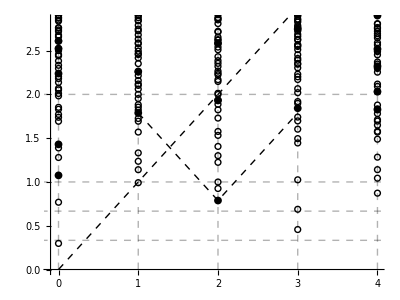

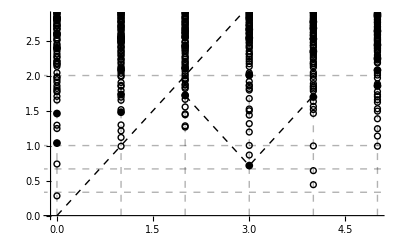

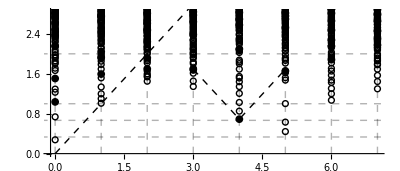

```mathematica
plots = Table[SpectrumIncludingFit[L0,j,3],{L0,8,14,3}]//Flatten;
Print[#]&/@plots;
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec8_ed.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec11_ed.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec14_ed.pdf",plots[[3]]];
(*Export["/Users/yinhslin/git/haagerup-chain/haagerup/spec17_ed.pdf",plots[[4]]];*)
```

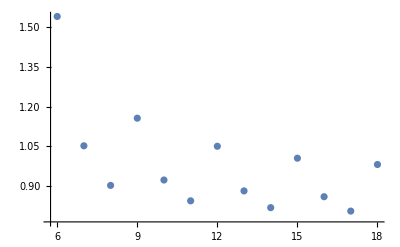

```mathematica
plot = ListPlot[Table[{L,ScaleFactor[L]},{L,6,18,1}],AxesLabel->{MaTeX["L",Magnification->1.5],MaTeX["\\gamma",Magnification->1.5]}]
```

```mathematica
SF = Interpolation[Table[{L,ScaleFactor[L]},{L,6,18,3}]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/gamma.pdf",plot];
```

### Shift-Z3 gauged theory

```mathematica
n = 9;
Table[k/n(1-k/n),{k,1,n-1}]//N
```

{0.0987654,0.17284,0.222222,0.246914,0.246914,0.222222,0.17284,0.0987654}

```mathematica
n = 6;
Table[k/n(1-k/n),{k,1,n-1}]//N
```

{0.138889,0.222222,0.25,0.222222,0.138889}

```mathematica
n = 3;
Table[k/n(1-k/n),{k,1,n-1}]//N
```

{0.222222,0.222222}

```mathematica
Join[Table[scalars[L][[1;;3]],{L,6,15,3}],Table[scalars[L][[2;;4]],{L,18,18,3}]]//MatrixForm
```

(0.462155 | 1.02017 | 1.4804
0.336642 | 0.802534 | 1.09651
0.302418 | 0.749261 | 0.987527
0.286585 | 0.729112 | 0.939172
0.277953 | 0.720201 | 0.913208)

```mathematica
Table[scalars[L][[1;;1]],{L,7,16,3}]
```

{{0.31547},{0.278019},{0.265218},{0.257495}}

```mathematica
Table[{L,scalars[L][[1]]},{L,7,16,3}]//MatrixForm
```

(7 | 0.31547
10 | 0.278019
13 | 0.265218
16 | 0.257495)

```mathematica
Table[{L,scalars[L][[1]]},{L,8,14,3}]//MatrixForm
```

(8 | 0.304959
11 | 0.276235
14 | 0.262155)

```mathematica
Join[Table[scalars[L][[1;;3]],{L,8,14,3}]]//MatrixForm
```

(0.304959 | 0.77641 | 1.28855
0.276235 | 0.741375 | 1.25866
0.262155 | 0.725373 | 1.22163)

### Open spectral analysis

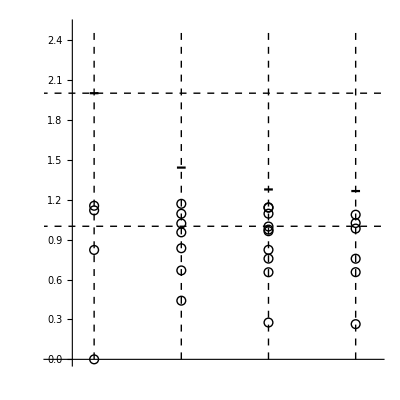

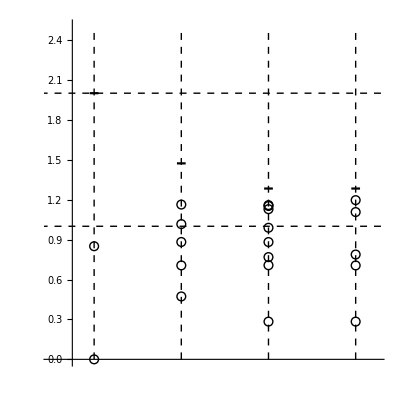

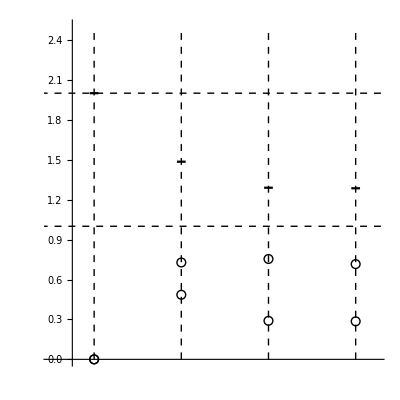

```mathematica
If[bc=="p",
Print["Change bc"];
,
plots = Table[OpenSpectrumIncludingFit[L0,j,q,"1e-08"],{L0,18,54,18}]//Flatten;
Print[#]&/@plots;
]
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/specOpen18.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/specOpen36.pdf",plots[[2]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/specOpen54.pdf",plots[[3]]];
```

```mathematica
Export["/Users/yinhslin/git/haagerup-chain/haagerup/specOpen18_1,-1,0.pdf",plots[[1]]];
Export["/Users/yinhslin/git/haagerup-chain/haagerup/specOpen36_1,-1,0.pdf",plots[[2]]];
```

### Open spectral analysis: Diagnose L=36 problem

```mathematica
spectra = {NSites[#]-1,ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==0&];
Energy = fitGSEnergy[gsEnergies,minL,"d",False];
```

```mathematica
2*Energy[36,#]&/@Transpose[Select[spectra,#[[1]]==36&][[1,2]]][[2]]//Sort
```

{0.000172664,0.644846,0.646682,1.07667,1.59511,1.61243,1.61803,1.74928,1.80242,1.93976,1.98341,2.02813,2.24458,2.35634,2.50828,2.51761,2.59845,2.62082,2.62356,2.62881,2.63182}

```mathematica
spectra = {NSites[#]-1,ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===q&];
Spec[L_] := Select[spectra,#[[1]]==L&][[1]];
```

```mathematica
2*CollectByRho[Energy,Spec[36]]//MatrixForm
```

({{1.99932,0.00091652},{1.99948,1.73092}}
{{-0.643956,1.07681},{-0.644034,1.61429},{-0.643576,2.00115}}
{{-1.07,0.655024},{-1.0699,1.58454},{-1.06944,1.7526},{-1.0698,1.89223},{-1.06938,2.17903}}
{{1.10856,0.654679},{1.10868,1.55301},{1.10726,1.7466}}
{{-0.661728,2.42909},{-1.05662,2.51304},{-0.415748,2.55064},{0.704494,2.55388},{1.1651,2.58943},{-0.93976,2.60635},{-0.313054,2.60703}})

## Golden

### Global variables

```mathematica
period = 2;
ζ = (1+Sqrt[5])/2;
{job,bc,maxdim,cutoff,j,u,q} = {"golden","p",1600,"1e-08","-1",2,0};
rs = If[bc=="p",{ζ,-1/ζ},{-1/ζ,1/ζ^2}];
cc = 0.7;
minL = 6;
```

### Dynamical exponent

```mathematica
(*
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,1]]-#[[2,1,1]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
*)
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gaps = {#[[1]]-If[bc=="p",0,1],#[[2,2,2]]-#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
maxL = Max[Transpose[gaps][[1]]];
gaps = Select[gaps,#[[1]]≥maxL/2&];
logGaps = {Log[#[[1]]],Log[#[[2]]]}&/@gaps;
lm = LinearModelFit[{#[[1]],#[[2]]}&/@logGaps,L,L];
c = FitParameterWithError[lm["ParameterTableEntries"][[1]]];
z = FitParameterWithError[lm["ParameterTableEntries"][[2]]];
```

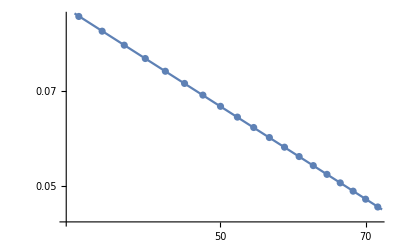

```mathematica
plot = Show[
ListLogLogPlot[gaps,AxesLabel->{MaTeX["L",Magnification->1.5],MaTeX["\\Delta E",Magnification->1.5]},
PlotLabel->MaTeX["\\begin{array}{c} \\text{\\bf "<>If[bc=="p","Periodic","Open"]<>"} \\\\ \\log(\\Delta E) = "<>z<>" \\log(L) + "<>c<>" \\end{array}",Magnification->1.5]],
Plot[lm[L],{L,Log[maxL/2]-0.01,Log[maxL]+0.01}]
]
```

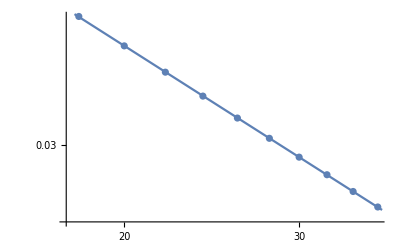

```mathematica
plot = Show[
ListLogLogPlot[gaps,AxesLabel->{MaTeX["L",Magnification->1.5],MaTeX["\\Delta E",Magnification->1.5]},
PlotLabel->MaTeX["\\begin{array}{c} \\text{\\bf "<>If[bc=="p","Periodic","Open"]<>"} \\\\ \\log(\\Delta E) = "<>z<>" \\log(L) + "<>c<>" \\end{array}",Magnification->1.5]],
Plot[lm[L],{L,Log[maxL/2]-0.01,Log[maxL]+0.01}]
]
```

### Central charge from entanglement entropy

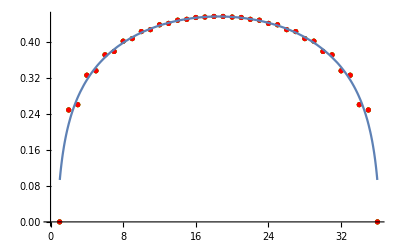

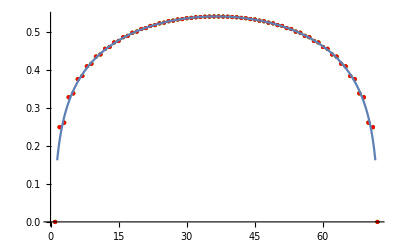

```mathematica
plots = AnalyzeEE[#]&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&&IntegerQ[(NSites[#]-If[BC[#]=="p",0,1])/If[BC[#]=="p",18,36]]&];
Print[#]&/@plots;
```

### Scaling dimension from energy

| Estimate | Standard Error | t-Statistic | P-Value
L | -0.76393 | 2.00916×10^-7 | -3.80223×10^6 | 8.23037×10^-177
1 | 0.580046 | 0.0000159581 | 36348.1 | 3.17789×10^-116
1/L | -0.157149 | 0.000313724 | -500.914 | 2.10343×10^-60
1/L^2 | 0.136142 | 0.00151539 | 89.8398 | 4.88772×10^-38

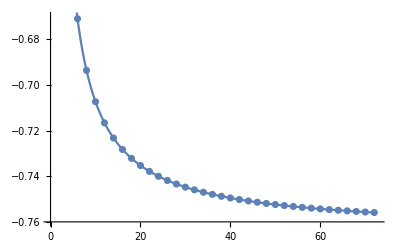

```mathematica
(*
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,1]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
*)
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
Energy = fitGSEnergy[gsEnergies,minL,bc,True];
```

| Estimate | Standard Error | t-Statistic | P-Value
L | -0.763908 | 3.08758×10^-6 | -247414. | 1.28032×10^-59
1 | -0.00159146 | 0.000153316 | -10.3803 | 2.38929×10^-7
1/L | -0.63049 | 0.00215543 | -292.512 | 1.71528×10^-24
1/L^2 | -0.302525 | 0.00853422 | -35.4484 | 1.62272×10^-13

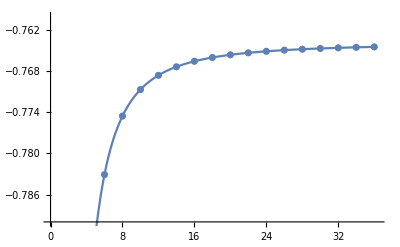

```mathematica
(*
spectra = {NSites[#],ReadData[#,"an"]}&/@Select[Labels["an"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,1]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
*)
spectra = {NSites[#],ReadData[#,"en"]}&/@Select[Labels["en"],Job[#]==job&&BC[#]==bc&&MaxDim[#]==maxdim&&Cutoff[#]==cutoff&&J[#]==j&&U[#]==u&&Charge[#]===0&];
gsEnergies = {#[[1]]-If[bc=="p",0,1],#[[2,1,2]]}&/@Select[spectra,Mod[#[[1]],period]==If[bc=="p",0,1]&];
Energy = fitGSEnergy[gsEnergies,minL,bc,True];
```

### Periodic spectral analysis

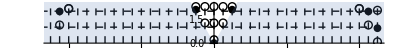

```mathematica
If[bc!="p",
Print["Change bc"];
,
plots = Table[SpectrumIncludingFit[L0,j,q],{L0,36,36,0}]//Flatten;
Print[#]&/@plots;
]
```

### Open spectral analysis

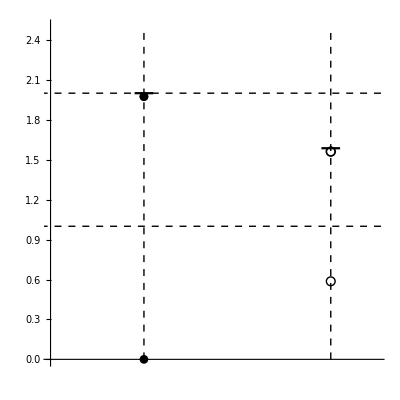

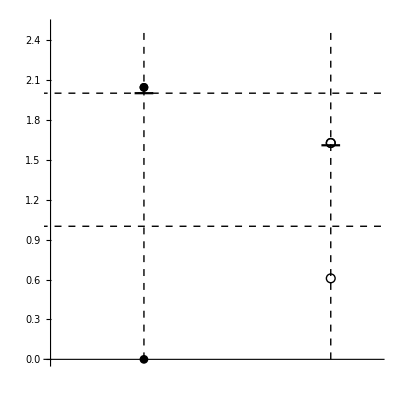

```mathematica
If[bc=="p",
Print["Change bc"];
,
plots = Table[OpenSpectrumIncludingFit[L0,j,q,"1e-08"],{L0,18,36,18}]//Flatten;
Print[#]&/@plots;
]
```